```mathematica
Clear["Global`*"]
```

```mathematica
M=1;λ=4*M;
l=2;m=2;
Ω=5*10^0/M;ω=m*Ω;
s=-I*λ*ω;
```

```mathematica
a[n_]:=a[n]=SeriesCoefficient[(σ(2-3σ)+s(1-2 σ^2))/(1-σ),{σ,0,n}];
b[n_]:=b[n]=SeriesCoefficient[(-(l(l+1)+σ(1+2s)+s^2(1+σ)))/(1-σ),{σ,0,n}];
c[n_]:=c[n]=If[n==0,1.0,If[n==1,-b[0]/a[0]c[0],-1/(n*a[0])(c[n-1]((n-1)(n-2)+b[0])+∑_(j=0)^(n-2) ((j+1)c[j+1]*a[n-j-1]+c[j]b[n-j-1]))]];
```

```mathematica
clist=Table[c[n],{n,1,200}];
```

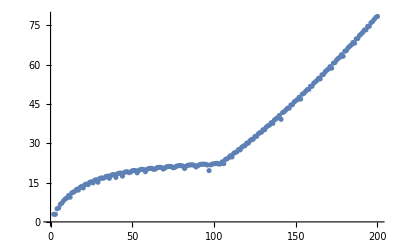

```mathematica
ListPlot[Log10[Abs[Re[clist]]]]
```

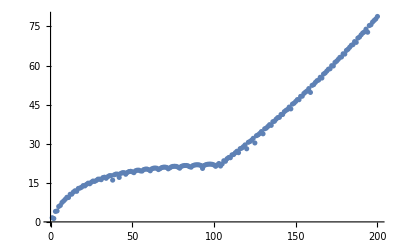

```mathematica
ListPlot[Log10[Abs[Im[clist]]]]
```

```mathematica
c[1]
```

0.-39.85 ⅈ

```mathematica
(σ(2-3σ)+s(1-2 σ^2))/σ^2/.{σ->1-t}//Simplify
```

((-1+40 ⅈ)+(4-160 ⅈ) t-(3-80 ⅈ) t^2)/(-1+t)^2

```mathematica
(-(l(l+1)+σ(1+2s)+s^2(1+σ)))/σ^2/.{σ->1-t}//Simplify
```

((3193+80 ⅈ)-(1599+80 ⅈ) t)/(-1+t)^2

```mathematica
α[n_]:=α[n]=SeriesCoefficient[(-1+4 t-3 t^2+s (-1+4 t-2 t^2))/(-1+t)^2,{t,0,n}];
β[n_]:=β[n]=SeriesCoefficient[(-1-l-l^2+s^2 (-2+t)+2 s (-1+t)+t)/(-1+t)^2,{t,0,n}];
γ[n_]:=γ[n]=If[n==0,1.0,1/(n(n-1-α[0]))(∑_(k=1)^n ((n-k)*α[k]+β[k-1])γ[n-k])];
```

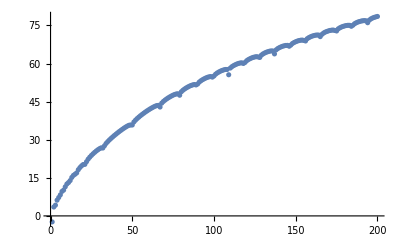

```mathematica
γlist=Table[γ[n],{n,1,200}];
ListPlot[Log10[Abs[Re[γlist]]]]
```

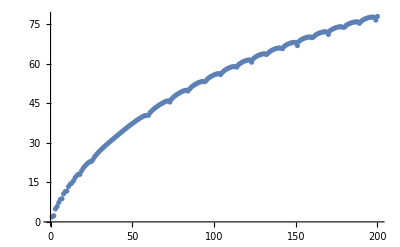

```mathematica
ListPlot[Log10[Abs[Im[γlist]]]]
```

```mathematica
DSolve[σ^2(*(1-σ)*)D[(D[(ϕ[σ]), σ]), σ]+((*σ(2-3σ)*)+s(1-2 σ^2))D[ϕ[σ], σ]-((*l(l+1)+σ*)+2s σ+s^2(1+σ))ϕ[σ]==0,ϕ[σ],{σ,0,1}]
```

{{ϕ[σ]→C[1] HeunD[s^2,-s (2+s),s,0,-2 s,σ]+ⅇ^(s (1/σ+2 σ)) σ^2 C[2] HeunD[-2+s^2,-((-2+s) s),-s,4,2 s,σ]}}

```mathematica
SeriesCoefficient[HeunD[-2+s^2,-((-2+s) s),-s,4,2 s,σ]/.{s->-10.0I},{σ,1,200}]
```

-5.572076373311×10^24-8.20825464873829×10^25 ⅈ

```mathematica
SeriesCoefficient[ⅇ^(s (1/σ+2 σ))/.{s->-10.0I},{σ,1,200}]
```

-1.63628×10^24-6.31834×10^23 ⅈ

```mathematica
SeriesCoefficient[HeunD[s^2,-s (2+s),s,0,-2 s,σ]/.{s->-10.0I},{σ,1,200}]
```

6.45059563662089×10^23-8.51503142869131×10^23 ⅈ

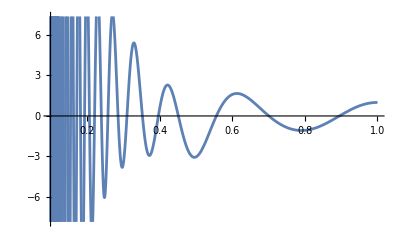

```mathematica
Plot[Re[HeunD[-2+s^2,-((-2+s) s),-s,4,2 s,σ]/.{s->-10.0I}],{σ,0.1,1}]
```

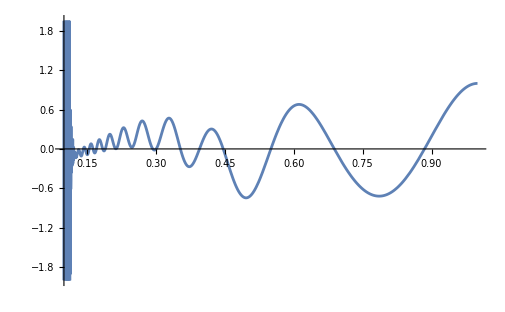

```mathematica
Plot[Re[HeunD[s^2,-s (2+s),s,0,-2 s,σ]/.{s->-10.0I}],{σ,0.1,1}]
```

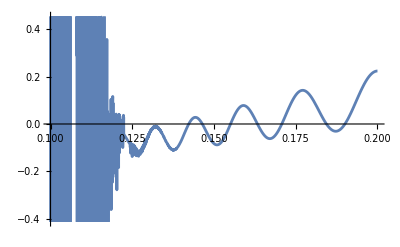

```mathematica
Plot[Re[HeunD[s^2,-s (2+s),s,0,-2 s,σ]/.{s->-10.0I}],{σ,0.1,0.2}]
```

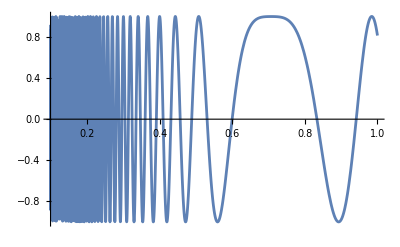

```mathematica
Plot[Re[ⅇ^(-(40 ⅈ (1+2 σ^2))/σ) ],{σ,0.1,1}]
```

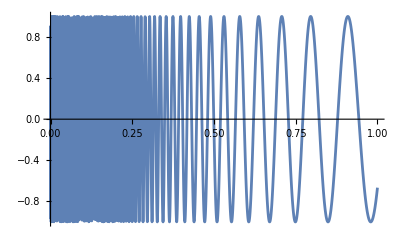

```mathematica
Plot[Re[ⅇ^(-(40 ⅈ)/σ) ],{σ,0,1}]
```

```mathematica
tmp=Table[SeriesCoefficient[ⅇ^(s/σ),{σ,1,n}],{n,0,200}];
```

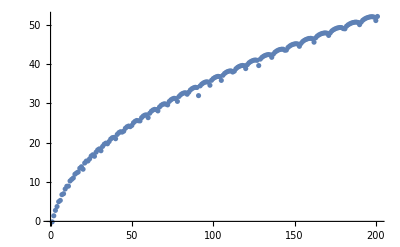

```mathematica
ListPlot[Log10[Abs[Im[tmp]]]]
```

```mathematica
Clear[s]
```

```mathematica
σ^2(1-σ)D[(D[(ⅇ^(s/σ)ϕ[σ]), σ]), σ]+(σ(2-3σ)+s(1-2 σ^2))(ⅇ^(s/σ)ϕ[σ])-(l(l+1)+σ+2s σ+s^2(1+σ))(ⅇ^(s/σ)ϕ[σ])/.{ϕ_[σ]->ϕ}//Simplify
```

-1/σ^2 ⅇ^(s/σ) ((σ^2 (6-σ+3 σ^2)+s^2 (-1+σ+σ^2+σ^3)+s σ (-2+σ+2 σ^2+2 σ^3)) ϕ-2 s (-1+σ) σ^2 ϕ'+(-1+σ) σ^4 ϕ'')

```mathematica
((σ^2 (6-σ+3 σ^2)+s^2 (-1+σ+σ^2+σ^3)+s σ (-2+σ+2 σ^2+2 σ^3)) ϕ-2 s (-1+σ) σ^2 ϕ'+(-1+σ) σ^4 ϕ'')/((-1+σ) σ^4)//Collect[#,{ϕ'',ϕ',ϕ}]&
```

((σ^2 (6-σ+3 σ^2)+s^2 (-1+σ+σ^2+σ^3)+s σ (-2+σ+2 σ^2+2 σ^3)) ϕ)/((-1+σ) σ^4)-(2 s ϕ')/σ^2+ϕ''

```mathematica
DSolve[((σ^2 (6-σ+3 σ^2)+s^2 (-1+σ+σ^2+σ^3)+s σ (-2+σ+2 σ^2+2 σ^3)) ϕ[σ])/((-1+σ) σ^4)-(2 s D[ϕ[σ], σ])/σ^2+D[D[ϕ[σ], σ], σ]==0,ϕ[σ],{σ,0.1,1}]
```

{{ϕ→}}

```mathematica
Series[-(2 s)/σ^2,{σ,1,4}]
```

-2 s+4 s (σ-1)-6 s (σ-1)^2+8 s (σ-1)^3-10 s (σ-1)^4+O[σ-1]^5

```mathematica
(σ^2 (6-σ+3 σ^2)+s^2 (-1+σ+σ^2+σ^3)+s σ (-2+σ+2 σ^2+2 σ^3))/.{σ->1}
```

8+3 s+2 s^2

```mathematica
Series[(σ^2 (6-σ+3 σ^2)+s^2 (-1+σ+σ^2+σ^3)+s σ (-2+σ+2 σ^2+2 σ^3))/((-1+σ) σ^4),{σ,1,4}]
```

(8+3 s+2 s^2)/(σ-1)+(-11+2 s-2 s^2)+(17-7 s) (σ-1)+(-23+14 s+5 s^2) (σ-1)^2+(29-23 s-14 s^2) (σ-1)^3+(-35+34 s+28 s^2) (σ-1)^4+O[σ-1]^5

```mathematica
s=-I*λ*ω;
```

```mathematica
ar[n_]:=ar[n]=SeriesCoefficient[-(2 s)/σ^2,{σ,1,n}];
br[n_]:=br[n]=SeriesCoefficient[(σ^2 (6-σ+3 σ^2)+s^2 (-1+σ+σ^2+σ^3)+s σ (-2+σ+2 σ^2+2 σ^3))/σ^4,{σ,1,n}];
cr[k_]:=cr[k]=If[k==0,1.0,-1/(k(k+1))∑_(j=0)^(k-1) (ar[j]*(k-j)+br[j])cr[k-j-1]];
```

```mathematica
crlist=Table[cr[n],{n,1,200}];
```

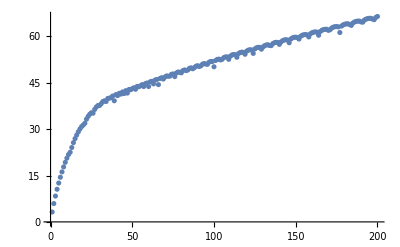

```mathematica
ListPlot[Log10[Abs[Re[crlist]]]]
```

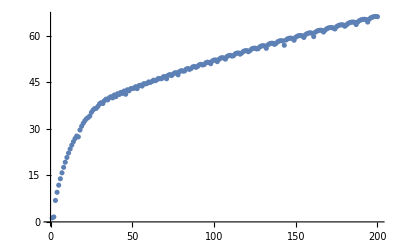

```mathematica
ListPlot[Log10[Abs[Im[crlist]]]]
```